```mathematica
dataG=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/gr.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataG//TableForm
```

N | L1 | L2 | D | 
1. | 167.61 | 179.85 | 1.5 | 0.01
2. | 163.87 | 183.575 | 3.88 | 0.03
3. | 161.195 | 186.11 | 6.21 | 0.05
4. | 159.16 | 188.135 | 8.4 | 0.07
5. | 157.385 | 189.965 | 10.61 | 0.09
6. | 155.82 | 191.55 | 12.77 | 0.11

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXG=MapAt[dropLastDot@*ToString,dataG,{{2;;,All}}];
forTeXG//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{N} & \text{L1} & \text{L2} & \text{D} & \text{} \\
 1 & 167.61 & 179.85 & 1.5 & 0.01 \\
 2 & 163.87 & 183.575 & 3.88 & 0.03 \\
 3 & 161.195 & 186.11 & 6.21 & 0.05 \\
 4 & 159.16 & 188.135 & 8.4 & 0.07 \\
 5 & 157.385 & 189.965 & 10.61 & 0.09 \\
 6 & 155.82 & 191.55 & 12.77 & 0.11 \\
\end{array}
\right)

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicksX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
myTicksY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
```

FittedModel[-0.644667+2.24943 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.644667 | 0.0831724 | -7.75097 | 0.00149282
x | 2.24943 | 0.0213567 | 105.327 | 4.87235×10^-8

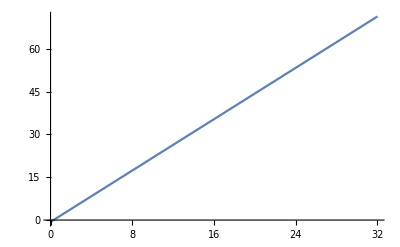

```mathematica
forFitG=dataG⟦2;;,{1,4}⟧;
fitG=LinearModelFit[forFitG,{1,x},x]
fitG@"ParameterTable"
Plot[fitG["Function"]@x, {x, 0, 32}]
```

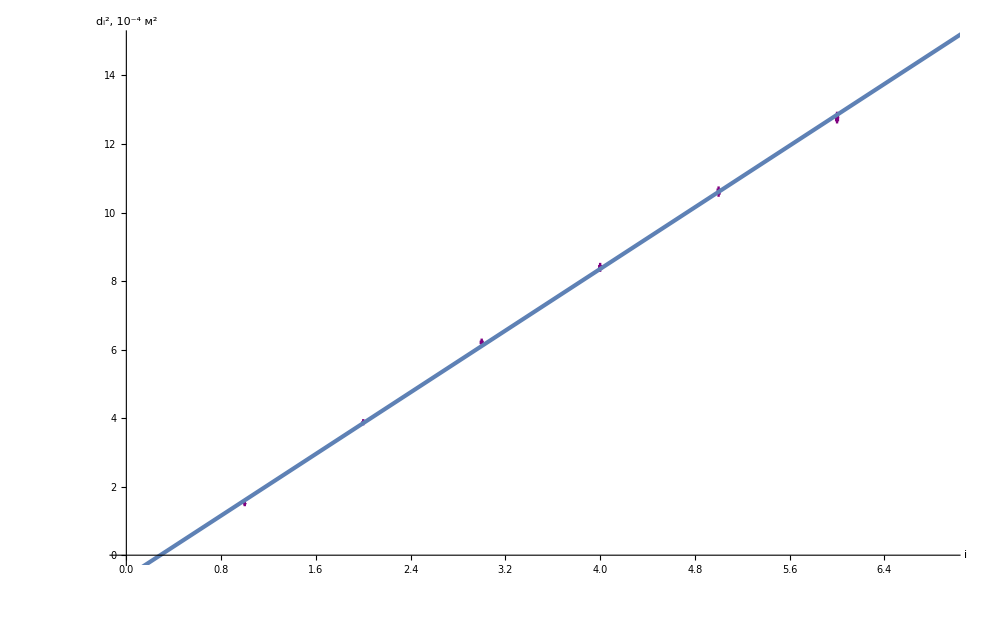

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataG⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"i","d_i^2, 10^-4 (:043c)^2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),(*horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)}],
PlotMarkers->{Automatic,0.01},Joined->False,PlotStyle->{Thickness@1.9, Purple},
PlotRange->{{0,6.9},{0,15}},
ImageSize->1000], Plot[fitG["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataY=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/ye.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataY//TableForm
```

N | Dср | dD | dD | 1/dD | 
2. | 15.7775 | 0.4 | 3.12 | 0.32 | 0.04
3. | 22.315 | 0.4 | 1.97 | 0.51 | 0.07
4. | 27.1525 | 0.4 | 1.68 | 0.6 | 0.1
5. | 30.9625 | 0.4 | 1.35 | 0.74 | 0.12
6. | 34.6 | 0.4 | 1.11 | 0.9 | 0.15

```mathematica
forTeXY=MapAt[dropLastDot@*ToString,dataY,{{2;;,All}}];
forTeXY//TeXForm
```

```mathematica
forFitY=dataY⟦2;;,{5,2}⟧;
fitY=LinearModelFit[forFitY,{1,x},x]
fitY@"ParameterTable"
Plot[fitY["Function"]@x, {x, 0, 1}]
```

FittedModel[5.84149+33.0945 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.84149 | 1.71922 | 3.39775 | 0.0425316
x | 33.0945 | 2.66548 | 12.416 | 0.00112585

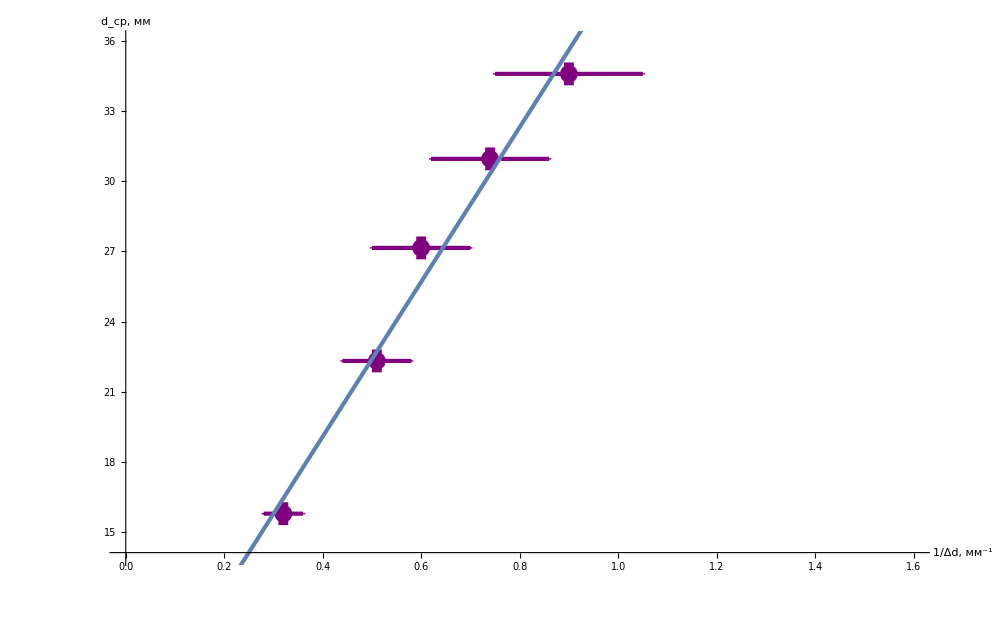

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataY⟦2;;,{5,2,6,3}⟧,
GridLines->{grids@0.25,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/Δd, (:043c:043c)^-1","d_(:0441:0440), мм"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,1.6},{14,36}},
ImageSize->1000], Plot[fitY["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.003]]
```

```mathematica
]
```

```mathematica
dataYT=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/yft.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataYT//TableForm
```

N | L1 | L2 | D | Dср | dD | dD | 1/dD | 
1. | 170.385 | 176.935 | 6.55 | 6.55 | 0.4 | 0. |  | 
2. | 166.66 | 180.88 | 14.22 | 15.7775 | 0.4 | 3.12 | 0.32 | 0.04
 | 164.94 | 182.275 | 17.335 |  |  |  |  | 
3. | 162.94 | 184.27 | 21.33 | 22.315 | 0.4 | 1.97 | 0.51 | 0.08
 | 161.995 | 185.295 | 23.3 |  |  |  |  | 
4. | 160.53 | 186.845 | 26.315 | 27.1525 | 0.4 | 1.68 | 0.6 | 0.12
 | 159.7 | 187.69 | 27.99 |  |  |  |  | 
5. | 158.365 | 188.95 | 30.585 | 30.9625 | 0.4 | 1.35 | 0.74 | 0.18
 | 157.69 | 189.03 | 31.34 |  |  |  |  | 
6. | 156.62 | 190.665 | 34.045 | 34.6 | 0.4 | 1.11 | 0.9 | 0.24
 | 156.09 | 191.245 | 35.155 |  |  |  |  |

```mathematica
forTeXYT=MapAt[dropLastDot@*ToString,dataYT,{{2;;,All}}];
forTeXYT//TeXForm
```

```mathematica
dataNa2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/na2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataNa2//TableForm
forTeXNa2=MapAt[dropLastDot@*ToString,dataNa2,{{2;;,All}}];
forTeXNa2//TeXForm
```

N | L1 | L2 | D |  | Dср |  | dD | 1/dD | 
1. | 148.89 | 140.49 | 8.4 | 0.71 | -- |  | - |  | 
2. | 152.29 | 137.27 | 15.03 | 2.26 | 16.14 | 0.59 | 2.22 | 0.45 | 0.05
 | 153.4 | 136.15 | 17.25 |  |  |  |  |  | 
3. | 155.29 | 134.13 | 21.16 | 4.48 | 21.97 | 0.59 | 1.61 | 0.62 | 0.07
 | 156.08 | 133.31 | 22.77 |  |  |  |  |  | 
4. | 157.62 | 131.77 | 25.85 | 6.68 | 26.46 | 0.59 | 1.22 | 0.82 | 0.09
 | 158.22 | 131.15 | 27.07 |  |  |  |  |  | 
5. | 159.61 | 129.85 | 29.76 | 8.86 | 30.33 | 0.59 | 1.13 | 0.88 | 0.12
 | 160.16 | 129.27 | 30.89 |  | 0. |  |  |  | 
6. | 161.17 | 128.11 | 33.06 | 10.93 | 33.56 | 0.59 | 1.01 | 0.99 | 0.14
 | 161.71 | 127.65 | 34.07 |  |  |  |  |  |

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{cccccccccc}
 \text{N} & \text{L1} & \text{L2} & \text{D} & \text{} & \text{D$\unicode{0441}\unicode{0440}$} & \text{} & \text{dD} & \text{1/dD} & \text{} \\
 1 & 148.89 & 140.49 & 8.4 & 0.71 & \text{--} & \text{} & - & \text{} & \text{} \\
 2 & 152.29 & 137.27 & 15.03 & 2.26 & 16.14 & 0.59 & 2.22 & 0.45 & 0.05 \\
 \text{} & 153.4 & 136.15 & 17.25 & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 3 & 155.29 & 134.13 & 21.16 & 4.48 & 21.97 & 0.59 & 1.61 & 0.62 & 0.07 \\
 \text{} & 156.08 & 133.31 & 22.77 & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 4 & 157.62 & 131.77 & 25.85 & 6.68 & 26.46 & 0.59 & 1.22 & 0.82 & 0.09 \\
 \text{} & 158.22 & 131.15 & 27.07 & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 5 & 159.61 & 129.85 & 29.76 & 8.86 & 30.33 & 0.59 & 1.13 & 0.88 & 0.12 \\
 \text{} & 160.16 & 129.27 & 30.89 & \text{} & 0 & \text{} & \text{} & \text{} & \text{} \\
 6 & 161.17 & 128.11 & 33.06 & 10.93 & 33.56 & 0.59 & 1.01 & 0.99 & 0.14 \\
 \text{} & 161.71 & 127.65 & 34.07 & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
\end{array}
\right)

```mathematica
dataNa1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/na2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataNa1//TableForm
```

FittedModel[-1.65667+2.08857 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.65667 | 0.192285 | -8.61567 | 0.000997617
x | 2.08857 | 0.0493743 | 42.3008 | 1.86699×10^-6

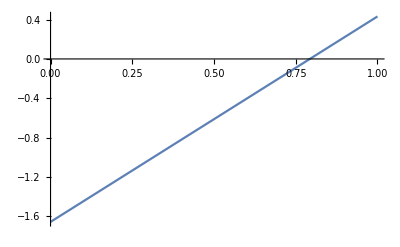

```mathematica
forFitNa1=dataNa1⟦2;;,{1,2}⟧;
fitNa1=LinearModelFit[forFitNa1,{1,x},x]
fitNa1@"ParameterTable"
Plot[fitNa1["Function"]@x, {x, 0, 1}]
```

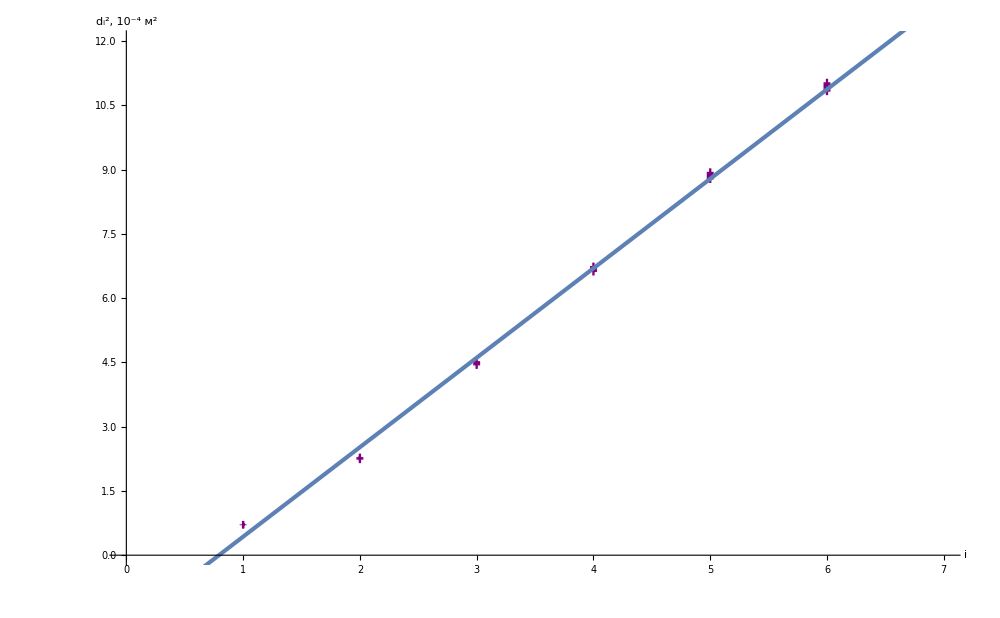

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataNa1⟦2;;,{1,2,3,3}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"i","d_i^2, 10^-4 (:043c)^2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),(*horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)}],
PlotMarkers->{Automatic,0.01},Joined->False,PlotStyle->{Thickness@1.9, Purple},
PlotRange->{{0,6.999},{0,11.999}},
ImageSize->1000], Plot[fitNa1["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

FittedModel[1.89638+31.6431 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.89638 | 1.66834 | 1.13668 | 0.338251
x | 31.6431 | 2.14888 | 14.7254 | 0.000679372

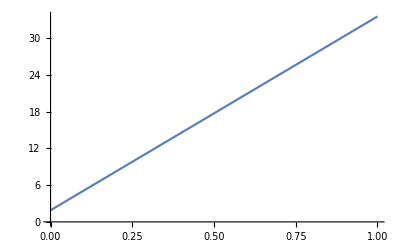

```mathematica
forFitNa2=dataNa1⟦2;;,{7,4}⟧;
fitNa2=LinearModelFit[forFitNa2,{1,x},x]
fitNa2@"ParameterTable"
Plot[fitNa2["Function"]@x, {x, 0, 1}]
```

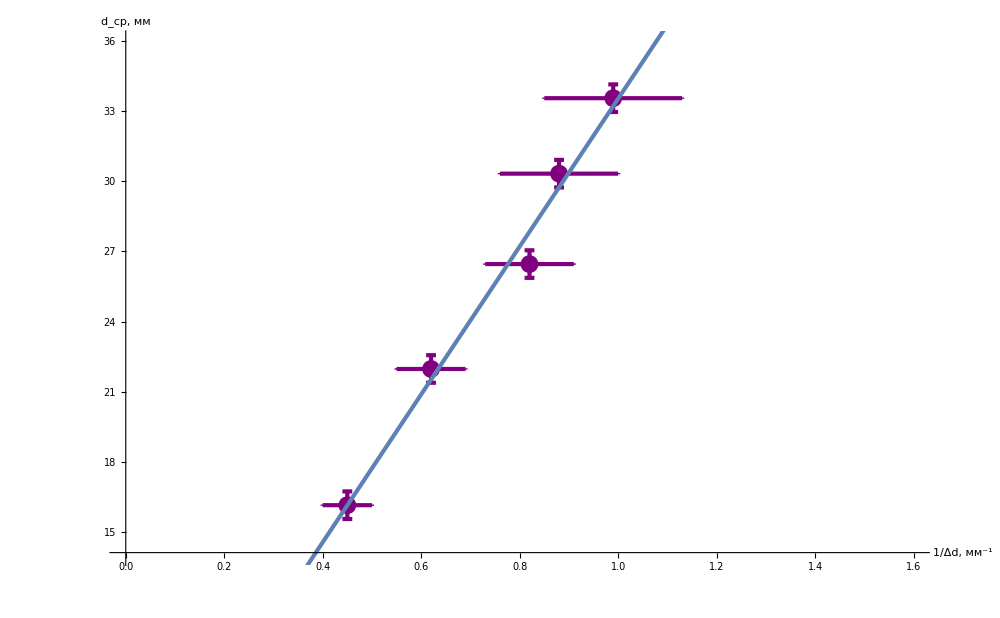

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataNa1⟦2;;,{7,4,8,5}⟧,
GridLines->{grids@0.25,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/Δd, (:043c:043c)^-1","d_(:0441:0440), мм"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,1.6},{14,36}},
ImageSize->1000], Plot[fitNa2["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataD=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/444/d.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataD//TableForm
forTeXD=MapAt[dropLastDot@*ToString,dataD,{{2;;,All}}];
forTeXD//TeXForm
```

3.12 | 0.39 | 15.78 | 0.27 | 2.22 | 0.2 | 16.14 | 0.19
1.97 | 0.25 | 22.32 | 0.19 | 1.61 | 0.14 | 21.97 | 0.14
1.68 | 0.21 | 27.15 | 0.15 | 1.22 | 0.11 | 26.46 | 0.11
1.35 | 0.17 | 30.96 | 0.14 | 1.13 | 0.1 | 30.33 | 0.1
1.11 | 0.14 | 34.6 | 0.12 | 1.01 | 0.09 | 33.56 | 0.09

\left(
\begin{array}{cccccccc}
 3.12 & 0.39 & 15.78 & 0.27 & 2.22 & 0.2 & 16.14 & 0.19 \\
 1.97 & 0.25 & 22.32 & 0.19 & 1.61 & 0.14 & 21.97 & 0.14 \\
 1.68 & 0.21 & 27.15 & 0.15 & 1.22 & 0.11 & 26.46 & 0.11 \\
 1.35 & 0.17 & 30.96 & 0.14 & 1.13 & 0.1 & 30.33 & 0.1 \\
 1.11 & 0.14 & 34.6 & 0.12 & 1.01 & 0.09 & 33.56 & 0.09 \\
\end{array}
\right)